# Runtime Testing

```mathematica
<<StoChemSim`
```

## Direct SSA

All system constructions have number of reactions = number of species.

```mathematica
(*System 1: Every species appears in precisely 1 reaction. Every reaction has only 1 reactant and 1 product.*)
ConstructSys1[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 2: Every species appears in O(sqrt(n)) reactions. Every reaction has O(sqrt(n)) reactants and O(sqrt(n)) products.*)
ConstructSys2[n_]:=Module[
{k,rxns,xConcs,yConcs,concs},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[Plus@@Table[x[i,l]+x[j,l],{l,k}],Plus@@Table[y[i,l]+y[j,l],{l,k}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xConcs=Flatten[Table[conc[x[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
yConcs=Flatten[Table[conc[y[ij,l],RandomInteger[100]],{ij,k},{l,k}]];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
(*System 3: Every species appears in all reactions. Every reaction has O(n) reactants and O(n) products.*)
ConstructSys3[n_]:=Module[
{rxns,xConcs,yConcs,concs},
rxns= Table[revrxn[Plus@@Table[x[j],{j,n}],Plus@@Table[y[j],{j,n}],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xConcs=Table[conc[x[i],RandomInteger[100]],{i,n}];
yConcs=Table[conc[y[i],RandomInteger[100]],{i,n}];
concs=Flatten[{xConcs,yConcs}];
{rxns,concs}]
```

```mathematica
TestSysSSA[construction_,kRange_,iters_,statesOnlyFlag_]:=Module[{},
Table[Module[
{n,rxns,concs,rxnsys,nRxns,nSpecies,results,totalTime,runtimeInfo,totalTimePerIter,algoTimePerIter,out},
n=k^2;
{rxns,concs} = construction[n];
rxnsys=Flatten[{rxns,concs}];
nRxns=Length[ExpandRevrxns[rxns]];
nSpecies=Length[SpeciesInRxnsys[rxnsys]];
results=Timing[SimulateDirectSSA[rxnsys,useIter->True,iterEnd->iters,statesOnly->statesOnlyFlag,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
totalTimePerIter=totalTime/iters;
runtimeInfo=GetRuntimeInfo[];
out={construction,statesOnlyFlag,nRxns,nSpecies,iters,totalTime,totalTimePerIter,runtimeInfo};
Print[out];
out],
{k,kRange}]]
```

## Constructions 1, 2, and 3 up to 50 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2,ConstructSys3};
kRange={1,3,5};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→7.6×10^-6,backend→0.0957441|>}

{ConstructSys1,False,18,18,100000,0.234375,2.34375×10^-6,<|frontend→0.015625,interface→0.0000887,backend→0.228297|>}

{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.015625,interface→0.0000676,backend→0.459948|>}

{ConstructSys1,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→3.5×10^-6,backend→0.11598|>}

{ConstructSys1,True,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000269,backend→0.210932|>}

{ConstructSys1,True,50,50,100000,0.421875,4.21875×10^-6,<|frontend→0.,interface→0.0000715,backend→0.41796|>}

{ConstructSys2,False,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→3.9×10^-6,backend→0.101979|>}

{ConstructSys2,False,18,18,100000,1.67188,0.0000167188,<|frontend→0.015625,interface→0.0000396,backend→1.66888|>}

{ConstructSys2,False,50,50,100000,5.78125,0.0000578125,<|frontend→0.,interface→0.0001475,backend→5.8402|>}

{ConstructSys2,True,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→4.5×10^-6,backend→0.095905|>}

{ConstructSys2,True,18,18,100000,1.5625,0.000015625,<|frontend→0.,interface→0.0000359,backend→1.57186|>}

{ConstructSys2,True,50,50,100000,5.04688,0.0000504688,<|frontend→0.015625,interface→0.0001057,backend→5.02562|>}

{ConstructSys3,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→4.3×10^-6,backend→0.133575|>}

{ConstructSys3,False,18,18,100000,5.17188,0.0000517188,<|frontend→0.,interface→0.0000652,backend→5.19861|>}

{ConstructSys3,False,50,50,100000,0.015625,1.5625×10^-7,<|frontend→0.015625,interface→0.0002088,backend→0.0012487|>}

{ConstructSys3,True,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→6.2×10^-6,backend→0.115964|>}

{ConstructSys3,True,18,18,100000,5.10938,0.0000510938,<|frontend→0.,interface→0.0000616,backend→5.2032|>}

{ConstructSys3,True,50,50,100000,53.5469,0.000535469,<|frontend→0.015625,interface→0.0004706,backend→56.2841|>}

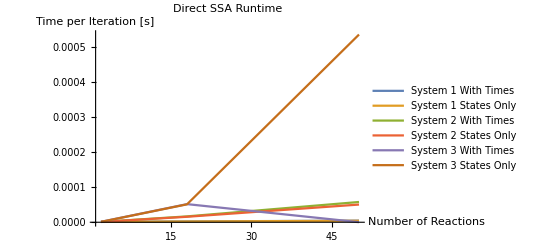

```mathematica
coorsSSA=Flatten[Table[
Table[{resultsSSA[[i]][[j]][[l]][[3]],resultsSSA[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2","System 3"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem], resultsSSA];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem], coorsSSA];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→7.6×10^-6,backend→0.0957441|>},{ConstructSys1,False,18,18,100000,0.234375,2.34375×10^-6,<|frontend→0.015625,interface→0.0000887,backend→0.228297|>},{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.015625,interface→0.0000676,backend→0.459948|>}},{{ConstructSys1,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→3.5×10^-6,backend→0.11598|>},{ConstructSys1,True,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000269,backend→0.210932|>},{ConstructSys1,True,50,50,100000,0.421875,4.21875×10^-6,<|frontend→0.,interface→0.0000715,backend→0.41796|>}}},{{{ConstructSys2,False,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→3.9×10^-6,backend→0.101979|>},{ConstructSys2,False,18,18,100000,1.67188,0.0000167188,<|frontend→0.015625,interface→0.0000396,backend→1.66888|>},{ConstructSys2,False,50,50,100000,5.78125,0.0000578125,<|frontend→0.,interface→0.0001475,backend→5.8402|>}},{{ConstructSys2,True,2,2,100000,0.09375,9.375×10^-7,<|frontend→0.,interface→4.5×10^-6,backend→0.095905|>},{ConstructSys2,True,18,18,100000,1.5625,0.000015625,<|frontend→0.,interface→0.0000359,backend→1.57186|>},{ConstructSys2,True,50,50,100000,5.04688,0.0000504688,<|frontend→0.015625,interface→0.0001057,backend→5.02562|>}}},{{{ConstructSys3,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→4.3×10^-6,backend→0.133575|>},{ConstructSys3,False,18,18,100000,5.17188,0.0000517188,<|frontend→0.,interface→0.0000652,backend→5.19861|>},{ConstructSys3,False,50,50,100000,0.015625,1.5625×10^-7,<|frontend→0.015625,interface→0.0002088,backend→0.0012487|>}},{{ConstructSys3,True,2,2,100000,0.109375,1.09375×10^-6,<|frontend→0.,interface→6.2×10^-6,backend→0.115964|>},{ConstructSys3,True,18,18,100000,5.10938,0.0000510938,<|frontend→0.,interface→0.0000616,backend→5.2032|>},{ConstructSys3,True,50,50,100000,53.5469,0.000535469,<|frontend→0.015625,interface→0.0004706,backend→56.2841|>}}}}

{{{2,9.375×10^-7},{18,2.34375×10^-6},{50,4.53125×10^-6}},{{2,1.25×10^-6},{18,2.1875×10^-6},{50,4.21875×10^-6}},{{2,9.375×10^-7},{18,0.0000167188},{50,0.0000578125}},{{2,9.375×10^-7},{18,0.000015625},{50,0.0000504688}},{{2,1.25×10^-6},{18,0.0000517188},{50,1.5625×10^-7}},{{2,1.09375×10^-6},{18,0.0000510938},{50,0.000535469}}}

## Constructions 1 and 2 up to 1,250 reactions

```mathematica
constructions={ConstructSys1,ConstructSys2};
kRange={1,3,5,10,25};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA2=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.15625,1.5625×10^-6,<|frontend→0.,interface→7.1×10^-6,backend→0.152396|>}

{ConstructSys1,False,18,18,100000,0.265625,2.65625×10^-6,<|frontend→0.,interface→0.0007363,backend→0.277308|>}

{ConstructSys1,False,50,50,100000,0.484375,4.84375×10^-6,<|frontend→0.,interface→0.0000736,backend→0.477807|>}

{ConstructSys1,False,200,200,100000,1.60938,0.0000160938,<|frontend→0.015625,interface→0.0002801,backend→1.75753|>}

{ConstructSys1,False,1250,1250,100000,10.5156,0.000105156,<|frontend→0.4375,interface→0.0026551,backend→10.8415|>}

{ConstructSys1,True,2,2,100000,0.15625,1.5625×10^-6,<|frontend→0.,interface→0.000019,backend→0.163837|>}

{ConstructSys1,True,18,18,100000,0.234375,2.34375×10^-6,<|frontend→0.,interface→0.0000272,backend→0.253075|>}

{ConstructSys1,True,50,50,100000,0.5,5.×10^-6,<|frontend→0.015625,interface→0.0000474,backend→0.502296|>}

{ConstructSys1,True,200,200,100000,1.6875,0.000016875,<|frontend→0.015625,interface→0.0003576,backend→1.6892|>}

{ConstructSys1,True,1250,1250,100000,10.125,0.00010125,<|frontend→0.390625,interface→0.0034707,backend→9.9137|>}

{ConstructSys2,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→7.3×10^-6,backend→0.124015|>}

{ConstructSys2,False,18,18,100000,1.78125,0.0000178125,<|frontend→0.,interface→0.0000376,backend→1.80253|>}

{ConstructSys2,False,50,50,100000,5.67188,0.0000567188,<|frontend→0.,interface→0.0001011,backend→5.71874|>}

{ConstructSys2,False,200,200,100000,28.7813,0.000287813,<|frontend→0.078125,interface→0.0008945,backend→30.0543|>}

{ConstructSys2,False,1250,1250,100000,1652.,0.01652,<|frontend→1.04688,interface→0.0104335,backend→1693.21|>}

{ConstructSys2,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.03125,interface→7.6×10^-6,backend→0.0952827|>}

{ConstructSys2,True,18,18,100000,1.46875,0.0000146875,<|frontend→0.,interface→0.0000886,backend→1.4573|>}

{ConstructSys2,True,50,50,100000,5.23438,0.0000523438,<|frontend→0.015625,interface→0.0001962,backend→5.23043|>}

{ConstructSys2,True,200,200,100000,27.1406,0.000271406,<|frontend→0.046875,interface→0.0004484,backend→27.2059|>}

{ConstructSys2,True,1250,1250,100000,238.734,0.00238734,<|frontend→0.984375,interface→0.0094418,backend→238.122|>}

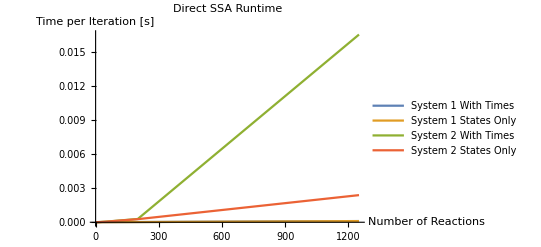

```mathematica
coorsSSA2=Flatten[Table[
Table[{resultsSSA2[[i]][[j]][[l]][[3]],resultsSSA2[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA2[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1","System 2"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA2,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem], resultsSSA2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem], coorsSSA2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA2.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.15625,1.5625×10^-6,<|frontend→0.,interface→7.1×10^-6,backend→0.152396|>},{ConstructSys1,False,18,18,100000,0.265625,2.65625×10^-6,<|frontend→0.,interface→0.0007363,backend→0.277308|>},{ConstructSys1,False,50,50,100000,0.484375,4.84375×10^-6,<|frontend→0.,interface→0.0000736,backend→0.477807|>},{ConstructSys1,False,200,200,100000,1.60938,0.0000160938,<|frontend→0.015625,interface→0.0002801,backend→1.75753|>},{ConstructSys1,False,1250,1250,100000,10.5156,0.000105156,<|frontend→0.4375,interface→0.0026551,backend→10.8415|>}},{{ConstructSys1,True,2,2,100000,0.15625,1.5625×10^-6,<|frontend→0.,interface→0.000019,backend→0.163837|>},{ConstructSys1,True,18,18,100000,0.234375,2.34375×10^-6,<|frontend→0.,interface→0.0000272,backend→0.253075|>},{ConstructSys1,True,50,50,100000,0.5,5.×10^-6,<|frontend→0.015625,interface→0.0000474,backend→0.502296|>},{ConstructSys1,True,200,200,100000,1.6875,0.000016875,<|frontend→0.015625,interface→0.0003576,backend→1.6892|>},{ConstructSys1,True,1250,1250,100000,10.125,0.00010125,<|frontend→0.390625,interface→0.0034707,backend→9.9137|>}}},{{{ConstructSys2,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.,interface→7.3×10^-6,backend→0.124015|>},{ConstructSys2,False,18,18,100000,1.78125,0.0000178125,<|frontend→0.,interface→0.0000376,backend→1.80253|>},{ConstructSys2,False,50,50,100000,5.67188,0.0000567188,<|frontend→0.,interface→0.0001011,backend→5.71874|>},{ConstructSys2,False,200,200,100000,28.7813,0.000287813,<|frontend→0.078125,interface→0.0008945,backend→30.0543|>},{ConstructSys2,False,1250,1250,100000,1652.,0.01652,<|frontend→1.04688,interface→0.0104335,backend→1693.21|>}},{{ConstructSys2,True,2,2,100000,0.125,1.25×10^-6,<|frontend→0.03125,interface→7.6×10^-6,backend→0.0952827|>},{ConstructSys2,True,18,18,100000,1.46875,0.0000146875,<|frontend→0.,interface→0.0000886,backend→1.4573|>},{ConstructSys2,True,50,50,100000,5.23438,0.0000523438,<|frontend→0.015625,interface→0.0001962,backend→5.23043|>},{ConstructSys2,True,200,200,100000,27.1406,0.000271406,<|frontend→0.046875,interface→0.0004484,backend→27.2059|>},{ConstructSys2,True,1250,1250,100000,238.734,0.00238734,<|frontend→0.984375,interface→0.0094418,backend→238.122|>}}}}

{{{2,1.5625×10^-6},{18,2.65625×10^-6},{50,4.84375×10^-6},{200,0.0000160938},{1250,0.000105156}},{{2,1.5625×10^-6},{18,2.34375×10^-6},{50,5.×10^-6},{200,0.000016875},{1250,0.00010125}},{{2,1.25×10^-6},{18,0.0000178125},{50,0.0000567188},{200,0.000287813},{1250,0.01652}},{{2,1.25×10^-6},{18,0.0000146875},{50,0.0000523438},{200,0.000271406},{1250,0.00238734}}}

## Construction 1 up to 20,000 reactions

```mathematica
constructions={ConstructSys1};
kRange={1,3,5,10,25,50,100};
iters=100000;
statesOnlyFlags={False,True};
resultsSSA3=Table[TestSysSSA[constructions[[i]],kRange,iters,statesOnlyFlags[[j]]],{i,Length[constructions]},{j,Length[statesOnlyFlags]}];
```

{ConstructSys1,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.015625,interface→6.9×10^-6,backend→0.10374|>}

{ConstructSys1,False,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000293,backend→0.215957|>}

{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.,interface→0.0000483,backend→0.442311|>}

{ConstructSys1,False,200,200,100000,1.5,0.000015,<|frontend→0.03125,interface→0.00015,backend→1.47598|>}

{ConstructSys1,False,1250,1250,100000,9.,0.00009,<|frontend→0.375,interface→0.0022468,backend→8.65393|>}

{ConstructSys1,False,5000,5000,100000,44.7656,0.000447656,<|frontend→4.25,interface→0.0499012,backend→40.3485|>}

{ConstructSys1,False,20000,20000,100000,232.813,0.00232813,<|frontend→63.375,interface→0.862514,backend→165.117|>}

{ConstructSys1,True,2,2,100000,0.1875,1.875×10^-6,<|frontend→0.03125,interface→7.1×10^-6,backend→0.149773|>}

{ConstructSys1,True,18,18,100000,0.296875,2.96875×10^-6,<|frontend→0.,interface→0.0007317,backend→0.3206|>}

{ConstructSys1,True,50,50,100000,0.421875,4.21875×10^-6,<|frontend→0.,interface→0.0001268,backend→0.424641|>}

{ConstructSys1,True,200,200,100000,1.48438,0.0000148438,<|frontend→0.03125,interface→0.0006861,backend→1.44959|>}

{ConstructSys1,True,1250,1250,100000,8.84375,0.0000884375,<|frontend→0.34375,interface→0.0055981,backend→8.47649|>}

{ConstructSys1,True,5000,5000,100000,41.1406,0.000411406,<|frontend→4.21875,interface→0.0434432,backend→36.7832|>}

{ConstructSys1,True,20000,20000,100000,226.359,0.00226359,<|frontend→59.125,interface→0.937623,backend→162.419|>}

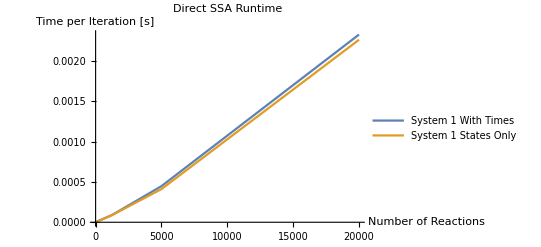

```mathematica
coorsSSA3=Flatten[Table[
Table[{resultsSSA3[[i]][[j]][[l]][[3]],resultsSSA3[[i]][[j]][[l]][[7]]},{l,Length[resultsSSA3[[i]][[j]]]}],
{i,Length[constructions]},{j,Length[statesOnlyFlags]}],1];
constructionLabels={"System 1"};
statesOnlyLabels={" With Times"," States Only"};
labelsSSA=Flatten[Table[constructionLabels[[i]]<>statesOnlyLabels[[j]],{i,Length[constructionLabels]},{j,Length[statesOnlyLabels]}],2];
ListLinePlot[
coorsSSA3,
PlotLegends->labelsSSA,
AxesLabel->{"Number of Reactions","Time per Iteration [s]"},
PlotLabel->"Direct SSA Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem], resultsSSA3];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem], coorsSSA3];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsSSA3.mx"},OperatingSystem->$OperatingSystem]]
coorsSSA3=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsSSA3.mx"},OperatingSystem->$OperatingSystem]]
```

{{{{ConstructSys1,False,2,2,100000,0.125,1.25×10^-6,<|frontend→0.015625,interface→6.9×10^-6,backend→0.10374|>},{ConstructSys1,False,18,18,100000,0.21875,2.1875×10^-6,<|frontend→0.,interface→0.0000293,backend→0.215957|>},{ConstructSys1,False,50,50,100000,0.453125,4.53125×10^-6,<|frontend→0.,interface→0.0000483,backend→0.442311|>},{ConstructSys1,False,200,200,100000,1.5,0.000015,<|frontend→0.03125,interface→0.00015,backend→1.47598|>},{ConstructSys1,False,1250,1250,100000,9.,0.00009,<|frontend→0.375,interface→0.0022468,backend→8.65393|>},{ConstructSys1,False,5000,5000,100000,44.7656,0.000447656,<|frontend→4.25,interface→0.0499012,backend→40.3485|>},{ConstructSys1,False,20000,20000,100000,232.813,0.00232813,<|frontend→63.375,interface→0.862514,backend→165.117|>}},{{ConstructSys1,True,2,2,100000,0.1875,1.875×10^-6,<|frontend→0.03125,interface→7.1×10^-6,backend→0.149773|>},{ConstructSys1,True,18,18,100000,0.296875,2.96875×10^-6,<|frontend→0.,interface→0.0007317,backend→0.3206|>},{ConstructSys1,True,50,50,100000,0.421875,4.21875×10^-6,<|frontend→0.,interface→0.0001268,backend→0.424641|>},{ConstructSys1,True,200,200,100000,1.48438,0.0000148438,<|frontend→0.03125,interface→0.0006861,backend→1.44959|>},{ConstructSys1,True,1250,1250,100000,8.84375,0.0000884375,<|frontend→0.34375,interface→0.0055981,backend→8.47649|>},{ConstructSys1,True,5000,5000,100000,41.1406,0.000411406,<|frontend→4.21875,interface→0.0434432,backend→36.7832|>},{ConstructSys1,True,20000,20000,100000,226.359,0.00226359,<|frontend→59.125,interface→0.937623,backend→162.419|>}}}}

{{{2,1.25×10^-6},{18,2.1875×10^-6},{50,4.53125×10^-6},{200,0.000015},{1250,0.00009},{5000,0.000447656},{20000,0.00232813}},{{2,1.875×10^-6},{18,2.96875×10^-6},{50,4.21875×10^-6},{200,0.0000148438},{1250,0.0000884375},{5000,0.000411406},{20000,0.00226359}}}

## Bounded Tau Leaping

```mathematica
<<StoChemSim`
```

```mathematica
ConstructSysMax[n_]:={
rxnl[{x1},{y,z1},1],
rxnl[{x2},{y,z2},1],
rxnl[{z1,z2},{k},1/n],
rxnl[{k,y},{},1/n],
conc[{x1,x2},n/2]
};
```

```mathematica
TestSysBTL[construction_,simulation_,nRange_]:=Module[{},
Table[Module[
{rxnsys,results,totalTime,runtimeInfo,algoTime},
rxnsys= construction[n];
results=Timing[simulation[rxnsys,finalOnly->True,outputTS->False]];
totalTime=results[[1]];
runtimeInfo=GetRuntimeInfo[];
out={simulation,n,totalTime,runtimeInfo};
Print[out];
out],
{n,nRange}]]
```

## Direct SSA vs. BTL up to 32,768 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[2^i,{i,1,15}];
resultsBTL=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,2,0.,<|frontend→0.,interface→0.0000105,backend→0.0003587|>}

{SimulateDirectSSA,4,0.,<|frontend→0.,interface→4.8×10^-6,backend→0.0000343|>}

{SimulateDirectSSA,8,0.,<|frontend→0.,interface→5.3×10^-6,backend→0.0002657|>}

{SimulateDirectSSA,16,0.,<|frontend→0.,interface→5.4×10^-6,backend→0.000097|>}

{SimulateDirectSSA,32,0.,<|frontend→0.,interface→6.7×10^-6,backend→0.000105|>}

{SimulateDirectSSA,64,0.,<|frontend→0.,interface→5.6×10^-6,backend→0.0006799|>}

{SimulateDirectSSA,128,0.,<|frontend→0.,interface→7.×10^-6,backend→0.0003755|>}

{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.3×10^-6,backend→0.0019275|>}

{SimulateDirectSSA,512,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0014971|>}

{SimulateDirectSSA,1024,0.015625,<|frontend→0.,interface→6.8×10^-6,backend→0.0041622|>}

{SimulateDirectSSA,2048,0.,<|frontend→0.,interface→7.4×10^-6,backend→0.0058785|>}

{SimulateDirectSSA,4096,0.,<|frontend→0.,interface→7.6×10^-6,backend→0.0131572|>}

{SimulateDirectSSA,8192,0.03125,<|frontend→0.,interface→7.9×10^-6,backend→0.0255962|>}

{SimulateDirectSSA,16384,0.0625,<|frontend→0.,interface→8.6×10^-6,backend→0.0659976|>}

{SimulateDirectSSA,32768,0.109375,<|frontend→0.,interface→0.0000117,backend→0.11402|>}

{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→8.7×10^-6,backend→0.0001456|>}

{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→6.4×10^-6,backend→0.0001201|>}

{SimulateBoundedTauLeaping,8,0.015625,<|frontend→0.015625,interface→0.0000126,backend→0.0002548|>}

{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→9.6×10^-6,backend→0.0004391|>}

{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→6.8×10^-6,backend→0.0008866|>}

{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→6.4×10^-6,backend→0.0017602|>}

{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→6.6×10^-6,backend→0.0035235|>}

{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.,interface→7.2×10^-6,backend→0.0083717|>}

{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→0.0000107,backend→0.0186721|>}

{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→0.0000102,backend→0.0184628|>}

{SimulateBoundedTauLeaping,2048,0.03125,<|frontend→0.,interface→0.0000118,backend→0.0212932|>}

{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→6.3×10^-6,backend→0.0327937|>}

{SimulateBoundedTauLeaping,8192,0.046875,<|frontend→0.,interface→7.8×10^-6,backend→0.0416795|>}

{SimulateBoundedTauLeaping,16384,0.046875,<|frontend→0.,interface→6.7×10^-6,backend→0.050693|>}

{SimulateBoundedTauLeaping,32768,0.078125,<|frontend→0.,interface→9.×10^-6,backend→0.075106|>}

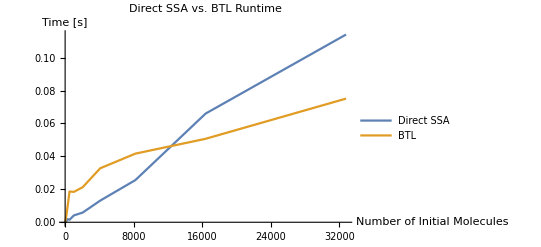

```mathematica
coorsBTL=Table[
Table[{resultsBTL[[i]][[l]][[2]],resultsBTL[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem], resultsBTL];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem], coorsBTL];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,2,0.,<|frontend→0.,interface→0.0000105,backend→0.0003587|>},{SimulateDirectSSA,4,0.,<|frontend→0.,interface→4.8×10^-6,backend→0.0000343|>},{SimulateDirectSSA,8,0.,<|frontend→0.,interface→5.3×10^-6,backend→0.0002657|>},{SimulateDirectSSA,16,0.,<|frontend→0.,interface→5.4×10^-6,backend→0.000097|>},{SimulateDirectSSA,32,0.,<|frontend→0.,interface→6.7×10^-6,backend→0.000105|>},{SimulateDirectSSA,64,0.,<|frontend→0.,interface→5.6×10^-6,backend→0.0006799|>},{SimulateDirectSSA,128,0.,<|frontend→0.,interface→7.×10^-6,backend→0.0003755|>},{SimulateDirectSSA,256,0.,<|frontend→0.,interface→5.3×10^-6,backend→0.0019275|>},{SimulateDirectSSA,512,0.,<|frontend→0.,interface→7.5×10^-6,backend→0.0014971|>},{SimulateDirectSSA,1024,0.015625,<|frontend→0.,interface→6.8×10^-6,backend→0.0041622|>},{SimulateDirectSSA,2048,0.,<|frontend→0.,interface→7.4×10^-6,backend→0.0058785|>},{SimulateDirectSSA,4096,0.,<|frontend→0.,interface→7.6×10^-6,backend→0.0131572|>},{SimulateDirectSSA,8192,0.03125,<|frontend→0.,interface→7.9×10^-6,backend→0.0255962|>},{SimulateDirectSSA,16384,0.0625,<|frontend→0.,interface→8.6×10^-6,backend→0.0659976|>},{SimulateDirectSSA,32768,0.109375,<|frontend→0.,interface→0.0000117,backend→0.11402|>}},{{SimulateBoundedTauLeaping,2,0.,<|frontend→0.,interface→8.7×10^-6,backend→0.0001456|>},{SimulateBoundedTauLeaping,4,0.,<|frontend→0.,interface→6.4×10^-6,backend→0.0001201|>},{SimulateBoundedTauLeaping,8,0.015625,<|frontend→0.015625,interface→0.0000126,backend→0.0002548|>},{SimulateBoundedTauLeaping,16,0.,<|frontend→0.,interface→9.6×10^-6,backend→0.0004391|>},{SimulateBoundedTauLeaping,32,0.,<|frontend→0.,interface→6.8×10^-6,backend→0.0008866|>},{SimulateBoundedTauLeaping,64,0.,<|frontend→0.,interface→6.4×10^-6,backend→0.0017602|>},{SimulateBoundedTauLeaping,128,0.,<|frontend→0.,interface→6.6×10^-6,backend→0.0035235|>},{SimulateBoundedTauLeaping,256,0.015625,<|frontend→0.,interface→7.2×10^-6,backend→0.0083717|>},{SimulateBoundedTauLeaping,512,0.015625,<|frontend→0.,interface→0.0000107,backend→0.0186721|>},{SimulateBoundedTauLeaping,1024,0.015625,<|frontend→0.,interface→0.0000102,backend→0.0184628|>},{SimulateBoundedTauLeaping,2048,0.03125,<|frontend→0.,interface→0.0000118,backend→0.0212932|>},{SimulateBoundedTauLeaping,4096,0.03125,<|frontend→0.,interface→6.3×10^-6,backend→0.0327937|>},{SimulateBoundedTauLeaping,8192,0.046875,<|frontend→0.,interface→7.8×10^-6,backend→0.0416795|>},{SimulateBoundedTauLeaping,16384,0.046875,<|frontend→0.,interface→6.7×10^-6,backend→0.050693|>},{SimulateBoundedTauLeaping,32768,0.078125,<|frontend→0.,interface→9.×10^-6,backend→0.075106|>}}}

{{{2,0.0003587},{4,0.0000343},{8,0.0002657},{16,0.000097},{32,0.000105},{64,0.0006799},{128,0.0003755},{256,0.0019275},{512,0.0014971},{1024,0.0041622},{2048,0.0058785},{4096,0.0131572},{8192,0.0255962},{16384,0.0659976},{32768,0.11402}},{{2,0.0001456},{4,0.0001201},{8,0.0002548},{16,0.0004391},{32,0.0008866},{64,0.0017602},{128,0.0035235},{256,0.0083717},{512,0.0186721},{1024,0.0184628},{2048,0.0212932},{4096,0.0327937},{8192,0.0416795},{16384,0.050693},{32768,0.075106}}}

## Direct SSA vs. BTL up to 1,000,000 molecules

```mathematica
simulations={SimulateDirectSSA,SimulateBoundedTauLeaping};
nRange=Table[10^i,{i,1,6}];
resultsBTL2=Table[TestSysBTL[ConstructSysMax,simulations[[i]],nRange],{i,Length[simulations]}];
```

{SimulateDirectSSA,10,0.,<|frontend→0.,interface→9.3×10^-6,backend→0.0013607|>}

{SimulateDirectSSA,100,0.,<|frontend→0.,interface→6.2×10^-6,backend→0.0002703|>}

{SimulateDirectSSA,1000,0.015625,<|frontend→0.,interface→5.7×10^-6,backend→0.0058601|>}

{SimulateDirectSSA,10000,0.03125,<|frontend→0.,interface→8.4×10^-6,backend→0.0359641|>}

{SimulateDirectSSA,100000,0.28125,<|frontend→0.,interface→7.2×10^-6,backend→0.282441|>}

{SimulateDirectSSA,1000000,2.67188,<|frontend→0.,interface→0.0000174,backend→2.66136|>}

{SimulateBoundedTauLeaping,10,0.,<|frontend→0.,interface→5.9×10^-6,backend→0.0002629|>}

{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→5.7×10^-6,backend→0.0028105|>}

{SimulateBoundedTauLeaping,1000,0.015625,<|frontend→0.,interface→5.4×10^-6,backend→0.0169744|>}

{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→0.0000121,backend→0.0493304|>}

{SimulateBoundedTauLeaping,100000,0.109375,<|frontend→0.,interface→0.0000101,backend→0.0955516|>}

{SimulateBoundedTauLeaping,1000000,0.25,<|frontend→0.,interface→7.4×10^-6,backend→0.257046|>}

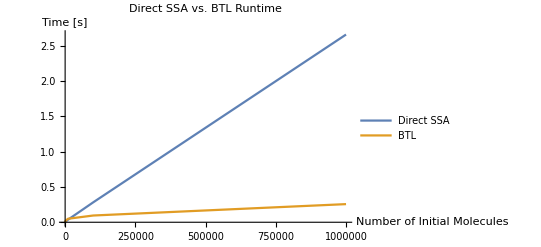

```mathematica
coorsBTL2=Table[
Table[{resultsBTL2[[i]][[l]][[2]],resultsBTL2[[i]][[l]][[4]]["backend"]},{l,Length[resultsBTL2[[i]]]}],
{i,Length[simulations]}];
simulationLabels={"Direct SSA","BTL"};
ListLinePlot[
coorsBTL2,
PlotLegends->simulationLabels,
AxesLabel->{"Number of Initial Molecules","Time [s]"},
PlotLabel->"Direct SSA vs. BTL Runtime",
PlotRange->All]
```

```mathematica
notebookPath=NotebookDirectory[];
Export[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem], resultsBTL2];
Export[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem], coorsBTL2];
```

```mathematica
notebookPath=NotebookDirectory[];
resultsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeResultsBTL2.mx"},OperatingSystem->$OperatingSystem]]
coorsBTL2=Import[FileNameJoin[{notebookPath,"mx\\runtimeCoorsBTL2.mx"},OperatingSystem->$OperatingSystem]]
```

{{{SimulateDirectSSA,10,0.,<|frontend→0.,interface→9.3×10^-6,backend→0.0013607|>},{SimulateDirectSSA,100,0.,<|frontend→0.,interface→6.2×10^-6,backend→0.0002703|>},{SimulateDirectSSA,1000,0.015625,<|frontend→0.,interface→5.7×10^-6,backend→0.0058601|>},{SimulateDirectSSA,10000,0.03125,<|frontend→0.,interface→8.4×10^-6,backend→0.0359641|>},{SimulateDirectSSA,100000,0.28125,<|frontend→0.,interface→7.2×10^-6,backend→0.282441|>},{SimulateDirectSSA,1000000,2.67188,<|frontend→0.,interface→0.0000174,backend→2.66136|>}},{{SimulateBoundedTauLeaping,10,0.,<|frontend→0.,interface→5.9×10^-6,backend→0.0002629|>},{SimulateBoundedTauLeaping,100,0.,<|frontend→0.,interface→5.7×10^-6,backend→0.0028105|>},{SimulateBoundedTauLeaping,1000,0.015625,<|frontend→0.,interface→5.4×10^-6,backend→0.0169744|>},{SimulateBoundedTauLeaping,10000,0.046875,<|frontend→0.,interface→0.0000121,backend→0.0493304|>},{SimulateBoundedTauLeaping,100000,0.109375,<|frontend→0.,interface→0.0000101,backend→0.0955516|>},{SimulateBoundedTauLeaping,1000000,0.25,<|frontend→0.,interface→7.4×10^-6,backend→0.257046|>}}}

{{{10,0.0013607},{100,0.0002703},{1000,0.0058601},{10000,0.0359641},{100000,0.282441},{1000000,2.66136}},{{10,0.0002629},{100,0.0028105},{1000,0.0169744},{10000,0.0493304},{100000,0.0955516},{1000000,0.257046}}}